```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
```

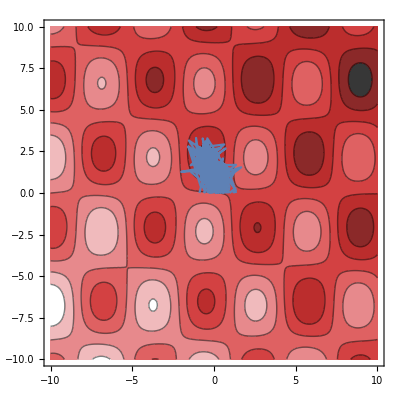
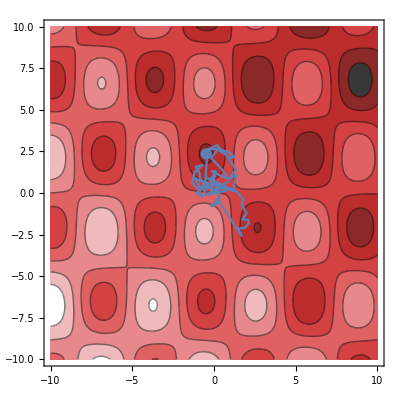
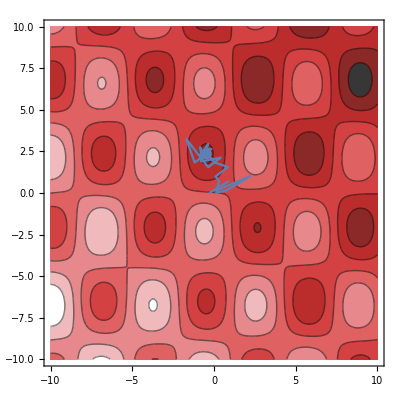
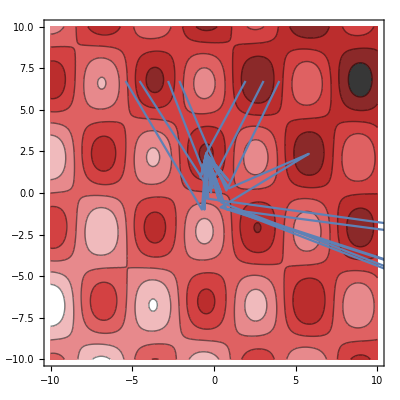
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Automatic | SimulatedAnnealing | DifferentialEvolution | NelderMead | RandomSearch

```mathematica
builtinMethods = {Automatic, "SimulatedAnnealing", "DifferentialEvolution", "NelderMead", "RandomSearch"};
vars = {x, y};
offset = {100, 100};
range = Sequence[{x, -10, 10}, {y, -10, 10}];
nicePlot[method_] := Module[{fun, solution, minima},
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
vars, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
Grid[{Map[nicePlot, builtinMethods], builtinMethods}]
```

```mathematica
Rasterize[%]
```

-Graphics-

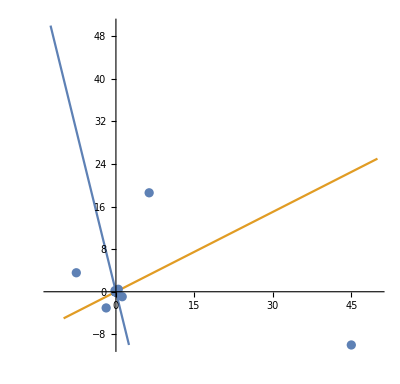

```mathematica
C1 = {-0.25, 1.0};
C2 = {1.0, 0.5};
P1 = Projection[#, C1] &;
P2 = Projection[#, C2] &;
β = 2.0;
f1 = (1 - 1/β) P1[#] + (1/β) # &;
f2 = (1 + 1/β) P2[#] - (1/β) # &;
f = #+ β(P1[f2[#]] - P2[f1[#]]) &;
DM[x_, it_] := Module[{t, i},
t = x;
For[i = 0, i < it, i++, t = Sow[f[t]]];
Return[t];
];
start = {45, -10};
{solution, {steps}} = Reap[DM[start, 50]];
Show[ParametricPlot[{u C1, u C2}, {u, -10, 50}], ListPlot[Prepend[steps, start]]]
```

```mathematica
C1 = {-0.25, 1.0, 2.25};
C2 = {1.0, 0.5, -0.25};
P1 = Projection[#, C1] &;
P2 = Projection[#, C2] &;
β = 2.5;
f1 = (1 - 1/β) P1[#] + (1/β) # &;
f2 = (1 + 1/β) P2[#] - (1/β) # &;
f = #+ β(P1[f2[#]] - P2[f1[#]]) &;
DM[x_, it_] := Module[{t, i},
t = x;
For[i = 0, i < it, i++, t = Sow[f[t]]];
Return[t];
];
start = {5, -10, 7};
{solution, {steps}} = Reap[DM[start, 15]];
Show[ParametricPlot3D[{u C1, u C2}, {u, -10, 45}], ListPointPlot3D[Prepend[steps, start], DataRange->Automatic]]
```

```mathematica
start = {4, 7};
other = {7, 8};
fun = N[griewankN[start]];
{fun2, solution} = FindMinimum[griewankN[{x, y}], {x, 4}, {y, 7}];
sol = {x, y} /. solution
Show[Plot3D[griewankN[{x, y}], {x, -10, 10}, {y, -10, 10}], ListPointPlot3D[{Join[start, {fun+0.01}],  Join[sol, {fun2+0.02}], Append[other, griewankN[other]]}]]
```

{3.14002,4.43844}

-Graphics3D-

```mathematica
solversToDo
(* `results` is loaded from DMData, but is a delayed assignment. By using an immediate assignment to `rs`, we force evaluation of `results`, collecting all the data we need. *)
rs = results;
```

{dm,sa,de,nm,rs}

```mathematica
ToAssociations[rules_] := Replace[rules, x : {__Rule} :> Association[x], {0, Infinity}];
as = ToAssociations[rs];
```

```mathematica
stats = ToAssociations[
Map[
Function[s,
s -> Map[
Function[r,
r -> With[{
funvs = Map[#["fun"] &, as[s][r]],
nfevs = Map[#["nfev"] &, as[s][r]]},
{"averageSolution" -> (Plus @@ funvs) / Length[funvs],
"medianSolution" -> Median@funvs,
"minimumSolution" -> Min @@ funvs,
"averageNfevs" -> N[(Plus @@ nfevs) / Length[nfevs]],
"medianNfevs" -> N[Median @ nfevs],
"minimumNfevs" -> N[Min @@ nfevs]
}]
], 
testFunctions[[;;,1]]]], 
(* Don't include the `auto` method in the analysis since we don't collect data for it by default.
The automatic method is just DifferentialEvolution or NelderMead, depending on the situation. *)
Cases[solvers[[;;,1]], Except["auto"]]
]
];
```

```mathematica
stats
```

<|dm→<|griewank→<|averageSolution→0.188428,medianSolution→0.16018,minimumSolution→0.012321,averageNfevs→31981.3,medianNfevs→32085.,minimumNfevs→29814.|>,rosenbrock→<|averageSolution→0.164159,medianSolution→1.26145×10^-6,minimumSolution→3.91008×10^-12,averageNfevs→68793.6,medianNfevs→70653.,minimumNfevs→18618.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→606.,medianNfevs→606.,minimumNfevs→606.|>,schaffer→<|averageSolution→11.7763,medianSolution→12.4946,minimumSolution→1.40795,averageNfevs→19795.7,medianNfevs→19743.,minimumNfevs→18150.|>,rastrigin→<|averageSolution→-1012.58,medianSolution→-1142.32,minimumSolution→-1520.4,averageNfevs→17081.,medianNfevs→15516.,minimumNfevs→354.|>,ackley→<|averageSolution→13.772,medianSolution→16.5592,minimumSolution→6.12986×10^-9,averageNfevs→5773.2,medianNfevs→3963.,minimumNfevs→2916.|>|>,sa→<|griewank→<|averageSolution→75.4387,medianSolution→60.6698,minimumSolution→1.28961,averageNfevs→116.06,medianNfevs→112.,minimumNfevs→92.|>,rosenbrock→<|averageSolution→0.51821,medianSolution→0.0000107425,minimumSolution→8.15227×10^-8,averageNfevs→813.48,medianNfevs→813.,minimumNfevs→812.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→811.,medianNfevs→811.,minimumNfevs→811.|>,schaffer→<|averageSolution→26.1798,medianSolution→26.3239,minimumSolution→12.804,averageNfevs→134.3,medianNfevs→132.,minimumNfevs→92.|>,rastrigin→<|averageSolution→-792.097,medianSolution→-764.239,minimumSolution→-1560.2,averageNfevs→806.4,medianNfevs→812.,minimumNfevs→732.|>,ackley→<|averageSolution→18.3882,medianSolution→19.0373,minimumSolution→11.3228,averageNfevs→106.2,medianNfevs→102.,minimumNfevs→92.|>|>,de→<|griewank→<|averageSolution→12.9051,medianSolution→4.63383,minimumSolution→0.0517797,averageNfevs→4045.,medianNfevs→4045.,minimumNfevs→4045.|>,rosenbrock→<|averageSolution→364.,medianSolution→0.0000127965,minimumSolution→2.99865×10^-7,averageNfevs→4046.6,medianNfevs→4046.,minimumNfevs→4045.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→3644.,medianNfevs→3644.,minimumNfevs→3644.|>,schaffer→<|averageSolution→25.7675,medianSolution→25.9345,minimumSolution→10.6241,averageNfevs→3845.18,medianNfevs→4045.,minimumNfevs→2046.|>,rastrigin→<|averageSolution→-1580.1,medianSolution→-1600.,minimumSolution→-1600.,averageNfevs→4013.,medianNfevs→4045.,minimumNfevs→2845.|>,ackley→<|averageSolution→8.62055,medianSolution→1.9793,minimumSolution→8.34793×10^-8,averageNfevs→4005.12,medianNfevs→4045.,minimumNfevs→2045.|>|>,nm→<|griewank→<|averageSolution→30.5388,medianSolution→11.3647,minimumSolution→0.221753,averageNfevs→189.66,medianNfevs→190.5,minimumNfevs→171.|>,rosenbrock→<|averageSolution→532.936,medianSolution→0.0000128602,minimumSolution→4.80778×10^-8,averageNfevs→176.88,medianNfevs→176.5,minimumNfevs→165.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→209.,medianNfevs→209.,minimumNfevs→209.|>,schaffer→<|averageSolution→26.1562,medianSolution→26.4686,minimumSolution→17.393,averageNfevs→172.02,medianNfevs→174.5,minimumNfevs→143.|>,rastrigin→<|averageSolution→-406.057,medianSolution→-644.843,minimumSolution→-1520.4,averageNfevs→184.54,medianNfevs→184.5,minimumNfevs→176.|>,ackley→<|averageSolution→17.0871,medianSolution→18.1205,minimumSolution→4.29848,averageNfevs→184.56,medianNfevs→185.,minimumNfevs→173.|>|>,rs→<|griewank→<|averageSolution→1.71839,medianSolution→0.989905,minimumSolution→0.128142,averageNfevs→163.42,medianNfevs→163.,minimumNfevs→163.|>,rosenbrock→<|averageSolution→3.4475×10^-6,medianSolution→2.5808×10^-6,minimumSolution→5.62271×10^-8,averageNfevs→226.12,medianNfevs→221.,minimumNfevs→210.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→123.,medianNfevs→123.,minimumNfevs→123.|>,schaffer→<|averageSolution→20.1005,medianSolution→20.1987,minimumSolution→7.81123,averageNfevs→170.9,medianNfevs→169.,minimumNfevs→164.|>,rastrigin→<|averageSolution→-747.523,medianSolution→-804.035,minimumSolution→-1520.4,averageNfevs→162.96,medianNfevs→163.,minimumNfevs→162.|>,ackley→<|averageSolution→15.3227,medianSolution→17.3194,minimumSolution→1.01488×10^-7,averageNfevs→164.18,medianNfevs→164.,minimumNfevs→163.|>|>|>